```mathematica
(* ::Package::*)

SetDirectory["C:\\Users\\heikkie13\\Work\\howard_scratches\\Mathematica"];
<<libs/FunctionsComplexAnalysis.m;
<<libs/FunctionsMatrixAnalysis.m;
<<libs/FunctionsFiniteGroups.m;
<<libs/FunctionsGF2.m
<<libs/FunctionsForExtraSpeciality.m;

(*This is needed for the unitary reps of symplectivc matrices:*)
(*<<"SymplecticBinary.m";*)

Clear[AllBinMats];
dB=10*Log[10,N[#]]&;
Clear[mm,rr]


(*These are needed for functions to work properly*)
(*The dimension for the simulation must be chosen here,as multiple data structures neede by decoders etc depend on m*)
mm=3;Nn=2^mm;InxBin=Tuples[{0,1},{mm}];WHn=WHmatrix[Nn]/Sqrt[Nn];InitializeVeryBare[mm];
Clear[Evaluate[Sequence@@Table["a"<>ToString[kk],{kk,1,mm}]]];
Clear[Evaluate[Sequence@@Table["b"<>ToString[kk],{kk,1,mm}]]];
avec=Table[ToExpression["a"<>ToString[kk]],{kk,1,mm}];
bvec=Table[ToExpression["b"<>ToString[kk]],{kk,1,mm}];
BitVec=Table[ToExpression["b"<>ToString[kk]],{kk,1,mm}];

(*All P-matrices for different ranks*)
PmatSets=Table[ComplementedBinarySubspaces[mm,rr],{rr,0,mm}];PmatSets[[2]]//mfl;
PmatInvSets=Table[Inverse[#,Modulus->2]&/@ComplementedBinarySubspaces[mm,rr],{rr,0,mm}];PmatInvSets[[2]]//mfl;

(*the binary Grassmann dimensions*)
BinGrassDims=QBinomial[mm,#,2]&/@(Range[mm+1]-1)
Plus@@BinGrassDims

(*These indicate the Schubert cell,for each rank,the position of the first non-zero element in the r first rows*)
BitInxs=Range[mm];
CellBitsAllRanks=Subsets[BitInxs,{#}]&/@(Range[mm+1]-1);

(*Preparing the indexing of all different matrices*)
MatricesPerRank=Table[QBinomial[mm,rr,2]*2^(rr (rr+1)/2),{rr,0,mm}]
tmp=0;MatThresh=AddTo[tmp,#]&/@MatricesPerRank;MatThreshAll=Join[{0},MatThresh];(*this is the total number of matrices*)Nmats=Plus@@MatricesPerRank;{Nmats,MatThreshAll[[-1]]}
MatThresh=Drop[MatThreshAll,-1];

(*The number of matrices of given rank for all possible index values is correct*)
(*Tally[(MatInx=#;rr=Flatten[Position[MatInx>#&/@MatThresh,True]][[-1]]-1)&/@Range[Nmats]];*)

CWsTot=Nn*Nmats
(*possible codewords/number of bits*)
Rate=Log[2,CWsTot]/Nn//N

ZeroVecm=Table[0,{mm}];
IntegerDigits[#-1,2,mm]&/@Range[2^mm]


(*all Pauli matrices are constructed from all combinations of an a-vec and a b-vec,each a m-dim binary vector*)
tups=Tuples[Range[2^mm],2];
(*the first index gives the binary a-vector,the second the binary b-vector*)
AllPaulis=(avec=IntegerDigits[#[[1]]-1,2,mm];
bvec=IntegerDigits[#[[2]]-1,2,mm];
MakePauli[avec,bvec])&/@tups;

AllPaulis//mfl;

Length[AllPaulis]

(*the corresponding 2m-dimensional binary vectors.*)
abvecs=(avec=IntegerDigits[#[[1]]-1,2,mm];
bvec=IntegerDigits[#[[2]]-1,2,mm];
Join[avec,bvec])&/@tups;

(*These are just the binary numbers[1,... Nn]-1*)
abvecs-(IntegerDigits[#-1,2,2mm]&/@Range[Nn^2])//Flatten//Union

(*these constitute a Frobenius-orthogonal complete basis for complex 2^m x 2^m matrices-Inner product matrix is proportional to identity*)
((first=ConjugateTranspose[#];Tr[first.#]/2^mm&/@AllPaulis)&/@AllPaulis)-IdentityMatrix[Nn^2]//Flatten//Union

(*All are Hermitian*)
(#-ConjugateTranspose[#])&/@AllPaulis//Flatten//Union

(*All are unitary*)
(#.ConjugateTranspose[#]-IdentityMatrix[Nn])&/@AllPaulis//Flatten//Union


(*Generate a set of projection matrices from the Paulis.These are projections as the Paulis are involutions*)
AllProjectors=(unitN+#)/2&/@AllPaulis;
(#.#-#)&/@AllProjectors//Flatten//Union


(*Generate a set of unitary matrices from the Paulis*)
(*These are Clifford group elemetns,and genererate Clifford*)
AllTransvecs=(unitN+I*#)/Sqrt[2]&/@AllPaulis;
(*these are indeed unitary*)
(ConjugateTranspose[#].#-unitN)&/@AllTransvecs//Flatten//Union


MakeUnitaryFromSymmetric=Module[{Sint,cvec,dvec,Ord2},Sint=#;
(cvec=IntegerDigits[#-1,2,mm];
Ord2=cvec.Sint.cvec;
(dvec=IntegerDigits[#-1,2,mm];
I^(Ord2+2 dvec.cvec)/Sqrt[2^mm])&/@Range[2^mm])&/@Range[2^mm]]&;


(*all symmetric m x m matrices.This function is in "FunctionsGF2"*)
AllBinSymm=GenerateSn2[mm];
AllUmats=MakeUnitaryFromSymmetric[#]&/@AllBinSymm;


CB=Transpose[Sequence@@(Transpose[#])&/@AllUmats];card=Length[CB[[1]]];{Length[AllUmats],card}


(*The permutations realizing the Howard shits are just the X-matrix acting in tensor dimension k*)
PermMatEShifts=TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]]&/@(Range[mm]-1);PermMatEShifts//mfl

(*The X-matrix acting in the first tensor dimension*)
(inx=#;avec=Table[0,{mm}];avec[[inx]]=1;MakePauli[avec,0*avec])&/@Range[mm]//mfl

(*the binary shift vectors*)
BinaryShifts=IntegerDigits[#,2,mm]&/@Table[Nn/2^kk,{kk,1,mm}]
(*The action of these shifts on the coordinates*)
(shift=#;FromDigits[Mod[IntegerDigits[#-1,2,mm]+shift,2],2]+1&/@Range[Nn])&/@BinaryShifts

(*The same shifts realized by permutation matrices*)
#.Range[Nn]&/@PermMatEShifts

(*The action of sum shifts on the coordinates*)
(shift=Plus@@(BinaryShifts[[#]]);FromDigits[Mod[IntegerDigits[#-1,2,mm]+shift,2],2]+1&/@Range[Nn])&/@{{2,1},{3,2}}
(*This is realized by sequential action of the permutation matrices*)
(*The order does not matter,as these permutators commute*)
(fir=#[[1]];sec=#[[2]];PermMatEShifts[[fir]].PermMatEShifts[[sec]].Range[Nn])&/@{{2,1},{3,2}}


DecodeRow=Module[{vecin,mu,Sest,signbits,tt,r,K,start,RangeNow,newK,wht,abses,signs,metrics,signbitsall,projectedvectors,Sests,peaks,peak,Sestk,metrick,PhaseVec,sigmak,signbitsk,Svec,avec,X,vecrot,veck,results,PermMatEsh,peaki,withProjections},Sest=#[[1]];
vecin=#[[2]];
signbits=#[[3]];
mu=#[[4]];
tt=#[[5]];
r=#[[6]];
K=#[[7]];
withProjections=#[[8]];
start=Transpose[Sest][[r]];
RangeNow=Pick[Range[2^mm],tt]+FromDigits[start,2];
(*In the end K might be greater than the number of possible different rows*)newK=Min[K,Length[RangeNow]];
(*Note:For precise correspondence as real number,one has to multiply with these!*)avec=ZeroVecm;avec[[r]]=1;
(*TODO ad-hoc phasevec,find out the reason why this works*)PhaseVec=(bvec=IntegerDigits[#-1,2,mm];I^(avec.bvec))&/@Range[Nn]//Chop;
PermMatEsh=PermMatEShifts[[r]];
wht=Sqrt[Nn]PhaseVec*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn//Chop;
abses=Abs[wht];
signs=Sign[wht];
metrics={};
signbitsall={};
projectedvectors={};
Sests={};
(*peaks=Reverse[Ordering[abses]];*)(*improve peaki computation maybe without comparisons*)peaks=Reverse[Sort[abses[[RangeNow]]]];
results={};
(k=#;
peaki=Position[abses,peaks[[k]]][[1,1]];
(*peak=peaks[[k]];*)(*Mathematica copies arrays by default so no worries of reference problems*)Sestk=Sest;
If[withProjections,metrick=(mu+abses[[peaki]])/2;,metrick=(mu+abses[[peaki]]);];
(*May give wrong result*)sigmak=signs[[peaki]];
signbitsk=signbits;
signbitsk[[r]]=(1+sigmak)/2;
Svec=IntegerDigits[peaki-1,2,mm];
Sestk[[r]]=Svec;
If[withProjections,avec=ZeroVecm;avec[[r]]=1;
(*construct the Pauli found,the sought for codeword is an eigenvector of this Pauli with eigenvalue+-1*)X=MakePauli[avec,Svec];
vecrot=X.vecin;
veck=(vecin+sigmak*vecrot)/2;,(*This runs if withProjections=False*)veck=vecin;];
results=Append[results,{Sestk,veck,signbitsk,metrick}];)&/@Range[newK];
results]&;


BreadthFirstDecoding=Module[{vecin,ordering,tt,Sest,K,candidatelist,newcandidates,r,inx,jnx,metrics,peakinxs,withProjections,vecest,posi,best,inners,cvec,candindices,shortrange},vecin=#[[1]];ordering=#[[2]];K=#[[3]];withProjections=#[[4]];
tt=Table[True,2^mm];
Sest=Table[0,{mm},{mm}];
candidatelist={{Table[0,{mm},{mm}],vecin,Table[0,mm],Norm[vecin]^2}};
(inx=#;
newcandidates={};
r=ordering[[inx]];
(jnx=#;
(*FOR FUTURE DEVELOPEMENT:If ordering is modified during the run,this needs to be improved*)newcandidates=Join[newcandidates,DecodeRow[Join[candidatelist[[jnx]],{tt,r,K,withProjections}]]];)&/@Range[Length[candidatelist]];
metrics=newcandidates[[Range[Length[newcandidates]],4]];
peakinxs=Reverse[Ordering[metrics]];
shortrange=Range[Min[K,Length[newcandidates]]];
candindices=peakinxs[[shortrange]];
candidatelist=newcandidates[[candindices]];
tt=UpdateTruthTable[{GiveTruthTable[{r,mm}],tt}];)&/@Range[mm];
If[withProjections,posi=1,inners=(best=#[[3]];best=1-best;Sest=#[[1]];
vecest=(cvec=IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec+2*best.cvec))&/@Range[Nn];vecest=vecest/Norm[vecest];
Abs[Conjugate[tstvec].vecest])&/@candidatelist;
posi=Position[inners,Max[inners]][[1,1]];];
candidatelist[[posi]]]&;


DecodingOrder=Module[{vecin,maxis,PermMatEsh,abses,permutetable},vecin=#;
maxis={};
(inx=#;
PermMatEsh=PermMatEShifts[[inx]];
abses=Abs[Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
maxis=Append[maxis,Max[abses]];)&/@Range[mm];
Reverse[Ordering[maxis]]]&;


Swap=Module[{tab,inx1,inx2,tmp},tab=#[[1]];inx1=#[[2]];inx2=#[[3]];
tmp=tab[[inx1]];
tab[[inx1]]=tab[[inx2]];
tab[[inx2]]=tmp;
tab]&;


DecodingOrder2=Module[{vecin,order},vecin=#;
order=DecodingOrder[vecin];
order=Swap[{order,1,2}];
order]&;


DecodingOrder3=Module[{vecin,order},vecin=#;
order=DecodingOrder[vecin];
order=Swap[{order,1,3}];
order]&;


DecodingOrder4=Module[{vecin,order},vecin=#;
order=DecodingOrder[vecin];
order=RotateRight[order,1];
order]&;


DecodingOrder5=Module[{vecin,order},vecin=#;
order=DecodingOrder[vecin];
order=RotateRight[order,2];
order=Swap[{order,1,2}];
order]&;


GiveTruthTable=Module[{index,size,basetable,binary},input=#;
index=#[[1]];
size=#[[2]];
binary=Mod[Floor[(Range[2^size]-1)/2^(size-index)],2];
Table[binary[[i]]==0,{i,1,2^size}]]&;
UpdateTruthTable=Module[{tt1,tt2},input=#;
tt1=#[[1]];
tt2=#[[2]];
Table[tt1[[i]]&&tt2[[i]],{i,1,Length[tt1]}]]&;
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

{1,7,7,1}

16

{1,14,56,64}

{135,135}

1080

1.2596

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

64

{0}

{0}

{0}

«3 more identical outputs»

{64,512}

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{{1,0,0},{0,1,0},{0,0,1}}

{{5,6,7,8,1,2,3,4},{3,4,1,2,7,8,5,6},{2,1,4,3,6,5,8,7}}

{{5,6,7,8,1,2,3,4},{3,4,1,2,7,8,5,6},{2,1,4,3,6,5,8,7}}

{{7,8,5,6,3,4,1,2},{4,3,2,1,8,7,6,5}}

{{7,8,5,6,3,4,1,2},{4,3,2,1,8,7,6,5}}

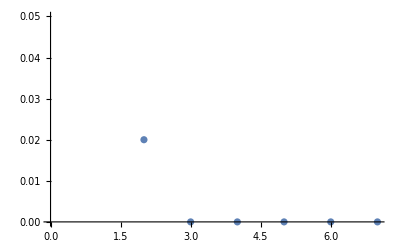

```mathematica
drops = 100;
Ktable = {1,2,3,4,5,20,512};
Errortable ={};
(K = #;
errors = 0;
(
tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = E^(I*2Pi*RandomReal[10, 8]); tstvec = tstvec/Norm[tstvec];
inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ClosestVec = Transpose[CB][[posi]];
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, Range[mm], K,True}];Sest //mf;
best = 1-best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Dist2 = 1-Abs[ClosestVec.Conjugate[vecest]]^2 ;
If[Abs[ClosestVec.Conj[vecest]]<= 0.99,errors = errors+1];
)&/@ Range[drops];
AppendTo[Errortable, errors];
)&/@Ktable;
ListPlot[Errortable/drops]
```

```mathematica
Errortable/drops // N
```

{0.13,0.05,0.04,0.02,0.,0.,0.}